```mathematica
Table[Indexed[a,i],{i,1,10}].Table[Indexed[b,i],{i,1,10}]
```

a1 b1+a2 b2+a3 b3+a4 b4+a5 b5+a6 b6+a7 b7+a8 b8+a9 b9+a10 b10

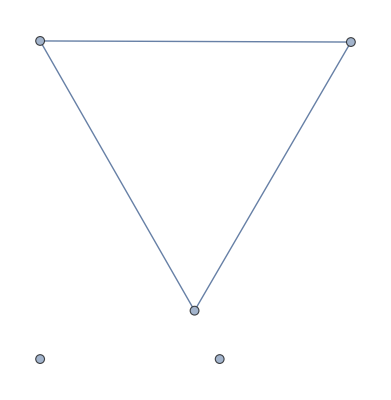

```mathematica
Graph[{1,2,3,4,5},{1<->2,1<->3,3<->2}]
```

```mathematica
Select[Keys[allGraphs5],IsomorphicGraphQ[Graph[{1,2,3,4,5},{1<->2,1<->3,3<->2}],allGraphs5[#,"graph"]]&]
```

{26487,21951,20439,8757,7293,2917,333,273,109,13}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,Select[Keys[allGraphs5],IsomorphicGraphQ[Graph[{1,2,3,4,5},{1<->2,1<->3,3<->2}],allGraphs5[#,"graph"]]&]}
]
```

{-Graphics-26487,-Graphics-21951,-Graphics-20439,-Graphics-8757,-Graphics-7293,-Graphics-2917,-Graphics-333,-Graphics-273,-Graphics-109,-Graphics-13}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,Select[Keys[allGraphs5],IsomorphicGraphQ[Graph[{1,2,3,4,5},{1<->2}],allGraphs5[#,"graph"]]&]}
]
```

{-Graphics-19683,-Graphics-6561,-Graphics-2187,-Graphics-729,-Graphics-243,-Graphics-81,-Graphics-27,-Graphics-9,-Graphics-3,-Graphics-1}

```mathematica
s123=With[
{searck=26487},
Table[k,{k,
Sort[Select[Keys[allGraphs5],allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
];
```

```mathematica
s12=With[
{searck=19683},
Table[k,{k,
Sort[Select[Keys[allGraphs5],allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
];
```

```mathematica
s23=With[
{searck=243},
Table[k,{k,
Sort[Select[Keys[allGraphs5],allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
];
```

```mathematica
s13=With[
{searck=6561},
Table[k,{k,
Sort[Select[Keys[allGraphs5],allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
];
```

```mathematica
{Length[s123],Length[s12],Length[s13],Length[s23]}
```

{351,127,127,127}

```mathematica
{Length[s123],Length[DeleteDuplicates[Join[s12,s13,s23]]]}
```

{351,351}

## Now the same but only orthogonal base vectors

```mathematica
s123=With[
{searck=26487},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{29767,49207,36085,29768,49208,49216,49210,36086,36166,36112,31954,30496,29857,29797,56011,51475,49963,38281,36817,49220,56012,51478,49972,36194,38308,36898,31984,32684,30586,29888,58288,56770,52232,39014,59048}

```mathematica
Length[s123]
```

35

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s123}
]
```

{-Graphics-29767,-Graphics-49207,-Graphics-36085,-Graphics-29768,-Graphics-49208,-Graphics-49216,-Graphics-49210,-Graphics-36086,-Graphics-36166,-Graphics-36112,-Graphics-31954,-Graphics-30496,-Graphics-29857,-Graphics-29797,-Graphics-56011,-Graphics-51475,-Graphics-49963,-Graphics-38281,-Graphics-36817,-Graphics-49220,-Graphics-56012,-Graphics-51478,-Graphics-49972,-Graphics-36194,-Graphics-38308,-Graphics-36898,-Graphics-31984,-Graphics-32684,-Graphics-30586,-Graphics-29888,-Graphics-58288,-Graphics-56770,-Graphics-52232,-Graphics-39014,-Graphics-59048}

```mathematica
s12=With[
{searck=19683},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{49207,49208,49216,49210,56011,51475,49963,49220,56012,51478,49972,58288,56770,52232,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s12}
]
```

{-Graphics-49207,-Graphics-49208,-Graphics-49216,-Graphics-49210,-Graphics-56011,-Graphics-51475,-Graphics-49963,-Graphics-49220,-Graphics-56012,-Graphics-51478,-Graphics-49972,-Graphics-58288,-Graphics-56770,-Graphics-52232,-Graphics-59048}

```mathematica
s13=With[
{searck=6561},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{36085,36086,36166,36112,56011,38281,36817,56012,36194,38308,36898,58288,56770,39014,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s13}
]
```

{-Graphics-36085,-Graphics-36086,-Graphics-36166,-Graphics-36112,-Graphics-56011,-Graphics-38281,-Graphics-36817,-Graphics-56012,-Graphics-36194,-Graphics-38308,-Graphics-36898,-Graphics-58288,-Graphics-56770,-Graphics-39014,-Graphics-59048}

```mathematica
s23=With[
{searck=243},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{29767,29768,31954,30496,29857,29797,56011,56012,31984,32684,30586,29888,58288,56770,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s23}
]
```

{-Graphics-29767,-Graphics-29768,-Graphics-31954,-Graphics-30496,-Graphics-29857,-Graphics-29797,-Graphics-56011,-Graphics-56012,-Graphics-31984,-Graphics-32684,-Graphics-30586,-Graphics-29888,-Graphics-58288,-Graphics-56770,-Graphics-59048}

```mathematica
{Length[s123],Length[DeleteDuplicates[Join[s12,s13,s23]]]}
```

{35,35}

```mathematica
Sort[DeleteDuplicates[Join[s12,s13,s23]]]==Sort[s123]
```

True

```mathematica
DeleteDuplicates[Intersection[s12,s13,s23]]
```

{56011,56012,56770,58288,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,DeleteDuplicates[Intersection[s12,s13,s23]]}
]
```

{-Graphics-56011,-Graphics-56012,-Graphics-56770,-Graphics-58288,-Graphics-59048}

## Now 3 edges not in a traingle

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,Select[Keys[allGraphs5],IsomorphicGraphQ[Graph[{1,2,3,4,5},{1<->2,1<->3,4<->5}],allGraphs5[#,"graph"]]&]}
]
```

{-Graphics-26245,-Graphics-21873,-Graphics-20421,-Graphics-19927,-Graphics-19767,-Graphics-19719,-Graphics-19695,-Graphics-19693,-Graphics-19687,-Graphics-8775,-Graphics-7371,-Graphics-6805,-Graphics-6669,-Graphics-6645,-Graphics-6643,-Graphics-6597,-Graphics-6589,-Graphics-3159,-Graphics-2457,-Graphics-2433,-Graphics-2431,-Graphics-2271,-Graphics-2223,-Graphics-2217,-Graphics-1053,-Graphics-981,-Graphics-973,-Graphics-819,-Graphics-813,-Graphics-765}

```mathematica
s12345=With[
{searck=26245},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{29525,49207,36085,29768,49208,49216,49210,36086,36166,36112,29537,29633,56011,51475,49963,38281,36817,32441,49220,56012,51478,49972,36194,38308,36898,32684,29888,58288,56770,52232,39014,59048}

```mathematica
Length[s12345]
```

32

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s12345}
]
```

{-Graphics-29525,-Graphics-49207,-Graphics-36085,-Graphics-29768,-Graphics-49208,-Graphics-49216,-Graphics-49210,-Graphics-36086,-Graphics-36166,-Graphics-36112,-Graphics-29537,-Graphics-29633,-Graphics-56011,-Graphics-51475,-Graphics-49963,-Graphics-38281,-Graphics-36817,-Graphics-32441,-Graphics-49220,-Graphics-56012,-Graphics-51478,-Graphics-49972,-Graphics-36194,-Graphics-38308,-Graphics-36898,-Graphics-32684,-Graphics-29888,-Graphics-58288,-Graphics-56770,-Graphics-52232,-Graphics-39014,-Graphics-59048}

```mathematica
s12=With[
{searck=19683},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{49207,49208,49216,49210,56011,51475,49963,49220,56012,51478,49972,58288,56770,52232,59048}

```mathematica
Length[s12]
```

15

```mathematica
Length[ListofVars[allGraphs5[19683,"colofour"]]]
```

37

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s12}
]
```

{-Graphics-49207,-Graphics-49208,-Graphics-49216,-Graphics-49210,-Graphics-56011,-Graphics-51475,-Graphics-49963,-Graphics-49220,-Graphics-56012,-Graphics-51478,-Graphics-49972,-Graphics-58288,-Graphics-56770,-Graphics-52232,-Graphics-59048}

```mathematica
s13=With[
{searck=6561},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{36085,36086,36166,36112,56011,38281,36817,56012,36194,38308,36898,58288,56770,39014,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s13}
]
```

{-Graphics-36085,-Graphics-36086,-Graphics-36166,-Graphics-36112,-Graphics-56011,-Graphics-38281,-Graphics-36817,-Graphics-56012,-Graphics-36194,-Graphics-38308,-Graphics-36898,-Graphics-58288,-Graphics-56770,-Graphics-39014,-Graphics-59048}

```mathematica
s45=With[
{searck=1},
Table[k,{k,
Sort[Select[allGraphs5AtomKeys,allGraphs5[#,"colofourvector"].allGraphs5[searck,"colofourvector"]==0&],CompKey]}]
]
```

{29525,29768,49208,36086,29537,29633,32441,49220,56012,36194,32684,29888,52232,39014,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,s45}
]
```

{-Graphics-29525,-Graphics-29768,-Graphics-49208,-Graphics-36086,-Graphics-29537,-Graphics-29633,-Graphics-32441,-Graphics-49220,-Graphics-56012,-Graphics-36194,-Graphics-32684,-Graphics-29888,-Graphics-52232,-Graphics-39014,-Graphics-59048}

```mathematica
{Length[s12345],Length[DeleteDuplicates[Join[s12,s13,s45]]]}
```

{32,32}

```mathematica
Sort[DeleteDuplicates[Join[s12,s13,s45]]]==Sort[s12345]
```

True

```mathematica
DeleteDuplicates[Intersection[s12,s13,s45]]
```

{56012,59048}

```mathematica
Table[
Labeled[allGraphs5[searck,"graph"],Style[searck,ColourForKey[allGraphs5,searck]]],
{searck,DeleteDuplicates[Intersection[s12,s13,s45]]}
]
```

{-Graphics-56012,-Graphics-59048}

```mathematica
Table[Table[allGraphs5[i,"colofourvector"].allGraphs5[j,"colofourvector"],{i,allGraphs5AtomKeys}],{j,allGraphs5AtomKeys}]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

## How many graphs are orthogonal to an atom

```mathematica
Table[Labeled[allGraphs5[j,"graph"],Style[j,ColourForKey[allGraphs5,j]]]->Total[Table[allGraphs5[i,"colofourvector"].allGraphs5[j,"colofourvector"],{i,Keys[allGraphs5]}]],{j,Sort[allGraphs5AtomKeys,CompKey]}]
```

{-Graphics-29524→1024,-Graphics-29525→576,-Graphics-29533→576,-Graphics-29527→576,-Graphics-29767→576,-Graphics-29605→576,-Graphics-29551→576,-Graphics-49207→576,-Graphics-36085→576,-Graphics-31711→576,-Graphics-30253→576,-Graphics-29768→328,-Graphics-29608→328,-Graphics-29560→328,-Graphics-49208→328,-Graphics-49216→328,-Graphics-49210→328,-Graphics-36086→328,-Graphics-36166→328,-Graphics-36112→328,-Graphics-31714→328,-Graphics-31954→328,-Graphics-31738→328,-Graphics-30262→328,-Graphics-30496→328,-Graphics-30334→328,-Graphics-29537→232,-Graphics-29857→232,-Graphics-29797→232,-Graphics-29633→232,-Graphics-56011→232,-Graphics-51475→232,-Graphics-49963→232,-Graphics-38281→232,-Graphics-36817→232,-Graphics-32441→232,-Graphics-49220→138,-Graphics-56012→138,-Graphics-51478→138,-Graphics-49972→138,-Graphics-36194→138,-Graphics-38308→138,-Graphics-36898→138,-Graphics-31984→138,-Graphics-32684→138,-Graphics-30586→138,-Graphics-29888→94,-Graphics-58288→94,-Graphics-56770→94,-Graphics-52232→94,-Graphics-39014→94,-Graphics-59048→52}